```mathematica
(* In this script, the neutrino transition probabilities are calculated and plotted. 
Notation wise, NH=Normal Hierarchy, IH=Inverted Hierarchy,EU=Early Universe and LU=Late Universe. We start by listing the parameters needed, which are retrieved from the ``Review of Particle Physics'', reference [32] of the manuscript.*)
Co[x_]:=Cos[x];
S[x_]:=Sin[x];
(*This is Subscript[θ, 12]*)
a=ArcSin[Sqrt[0.307]];
(*This is Subscript[θ, 13]*)
b=ArcSin[Sqrt[0.0218]];
(*This is Subscript[θ, 23] in the NH*)
NHc=ArcSin[Sqrt[0.545]];
(*This is Subscript[θ, 23] in the IH*)
IHc=ArcSin[Sqrt[0.547]];
(*CP violating phase δ*)
d=1.36*Pi;
(*Subscript[Δm, 21]^2=Subscript[m, 2]^2-Subscript[m, 1]^2*)
Dm21=7.53;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the IH*)
Dm32IH=-2.546;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the NH*)
Dm32NH=2.453;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the NH*)
Dm31NH=Dm32NH+Dm21;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the IH*)
Dm31IH=Dm32IH+Dm21;
(*This is a typical neutrino energy detected at neutrino observatories. As long as the value is high enough to be in the ultra-high energy regime, the excat value does not affect the results*)
E0=10^16.;
(*In natural units, Subscript[H, 0]=2.13 x10^-33 xh. We keep this infinitesimal prefactor seperate to better study the effect of choosing different h. In reality 
this prefactor can be cast away by a renormalization of the scale factor and redshift*)
H0=2.13*10^-33.;
(*Matter density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, m0]*)
Om0=0.315;
(*Dark Energy(DE) density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, Λ0]*)
Ol0=0.685;
(*Hubble parameter at EU, i.e. h^EU*)
EUh=0.675;
(*Hubble parameter at LU, i.e. h^LU*)
LUh=0.732;
(*This is the integrand in eq.(11) of the mansucript*)
Subscript[F, Λ][z_]:= (Om0*(1+z)^7.+Ol0*(1+z)^4.)^-.5;
int=Assuming[z>=0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]];
(*This is Δλ of the mnasucript, eq.(11), for EU*)
EUomAn=int/EUh;
(*This is Δλ of the mnasucript, eq.(11), for LU*)
LUomAn=int/LUh;
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
NHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[NHc]-S[b]*S[NHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[NHc]-S[a]*S[NHc]*S[b]*(Co[d]+I*S[d]),S[NHc]*Co[b]},{S[a]*S[NHc]-S[b]*Co[a]*Co[NHc]*(Co[d]+I*S[d]),-S[NHc]*Co[a]-S[a]*S[b]*Co[NHc]*(Co[d]+I*S[d]),Co[b]*Co[NHc]}};
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
IHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[IHc]-S[b]*S[IHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[IHc]-S[a]*S[IHc]*S[b]*(Co[d]+I*S[d]),S[IHc]*Co[b]},{S[a]*S[IHc]-S[b]*Co[a]*Co[IHc]*(Co[d]+I*S[d]),-S[IHc]*Co[a]-S[a]*S[b]*Co[IHc]*(Co[d]+I*S[d]),Co[b]*Co[IHc]}};
```

```mathematica
(*U^† for NH*)
NHUdag=ConjugateTranspose[NHU];
(*U^† for IH*)
IHUdag=ConjugateTranspose[IHU];
(*The fllowing two lines are to check the Unitarity condition of the PMNS matrix, to make sure there was no error in writing them, for both NH and IH*)
MatrixForm[FullSimplify[NHUdag . NHU]];
MatrixForm[FullSimplify[IHUdag . IHU]];
```

```mathematica
(*Initial conditions: {1,0,0} for Neutron Decay; {0,1,0} for Muon Damping; {1/Sqrt[5],2/Sqrt[5],0} for Pion Decay*)
Psi0={1/Sqrt[5],2/Sqrt[5],0};
```

```mathematica
(*Initial condition for transition amplitude in the mass basis, Φ of the manuscript, in the NH and IH, respectively. Basically eq.(8) of the manuscript*)
NHPhi0=NHUdag . Psi0;
IHPhi0=IHUdag . Psi0;
```

```mathematica
(*The evolving factors for the mass basis transition amplitudes, as written in eq.(10) of the mnasucript*)
T=DiagonalMatrix[{Co[m1^2*Intz/2]-I*S[m1^2*Intz/2],Co[m2^2*Intz/2]-I*S[m2^2*Intz/2],Co[m3^2*Intz/2]-I*S[m3^2*Intz/2]}];
(*The evolved transition amplitude, in the mass basis, with redshift, as given in eq.(10) of the mansucript, for NH and IH, respectively*)
NHPhi=FullSimplify[T.NHPhi0];
IHPhi=FullSimplify[T.IHPhi0];
```

```mathematica
(*The evolved transition amplitude, in the flavor basis, with redshift, as given in eq.(10) of the mansucript, for NH and IH, respectively*)
NHPsi=NHU . NHPhi;
IHPsi=IHU . IHPhi;
(*Analytical expression for transition probability to Subscript[ν, e] for NH and IH, respectively*)
Print["NHPee="]
NHPee=FullSimplify[TrigReduce[ComplexExpand[Re[NHPsi[[1]]]^2+Im[NHPsi[[1]]]^2]]]
Print["IHPee="]
IHPee=FullSimplify[TrigReduce[ComplexExpand[Re[IHPsi[[1]]]^2+Im[IHPsi[[1]]]^2]]]
(*Analytical expression for transition probability to Subscript[ν, μ] for NH and IH, respectively*)
Print["NHPemu="]
NHPemu=FullSimplify[TrigReduce[ComplexExpand[Re[NHPsi[[2]]]^2+Im[NHPsi[[2]]]^2]]]
Print["IHPemu="]
IHPemu=FullSimplify[TrigReduce[ComplexExpand[Re[IHPsi[[2]]]^2+Im[IHPsi[[2]]]^2]]]
(*Analytical expression for transition probability to Subscript[ν, τ] for NH and IH, respectively*)
Print["NHPetau="]
NHPetau=FullSimplify[TrigReduce[ComplexExpand[Re[NHPsi[[3]]]^2+Im[NHPsi[[3]]]^2]]]
Print["IHPetau="]
IHPetau=FullSimplify[TrigReduce[ComplexExpand[Re[IHPsi[[3]]]^2+Im[IHPsi[[3]]]^2]]]
```

NHPee=

0.194345+0.0508403 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0140805 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0311048 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0480265 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00605253 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0719836 Sin[1/2 Intz (m2-m3) (m2+m3)]

IHPee=

0.193977+0.0513411 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0141689 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.031149 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0480087 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00616949 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0720097 Sin[1/2 Intz (m2-m3) (m2+m3)]

NHPemu=

0.418559-0.0145874 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0180778 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.414106 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0279657 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0261133 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0519228 Sin[1/2 Intz (m2-m3) (m2+m3)]

IHPemu=

0.418753-0.0146994 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0183137 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.41426 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0279293 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0262489 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0519304 Sin[1/2 Intz (m2-m3) (m2+m3)]

NHPetau=

0.387096-0.0362529 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0321582 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.383001 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0200608 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0200608 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0200608 Sin[1/2 Intz (m2-m3) (m2+m3)]

IHPetau=

0.38727-0.0366417 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0324826 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.383111 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0200794 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0200794 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0200794 Sin[1/2 Intz (m2-m3) (m2+m3)]

```mathematica
(*Now that we have the general analytical expressions, we start specifiying for the cases EU and LU for each neutrino flavor. That is, we substitute the argument of the trigonometric functions that appeared before with the appropriate Δm^2 xΔλ for the four cases NH-EU, NH-LU, IH-EU,IH-LU*)
```

```mathematica
(*NHEU*)
```

```mathematica
newPeeNHEU[z_]=NHPee/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*EUomAn};
newPemuNHEU[z_]=NHPemu/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*EUomAn};
newPetauNHEU[z_]=NHPetau/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*EUomAn};
```

```mathematica
(*NHLU*)
```

```mathematica
newPeeNHLU[z_]=NHPee/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*LUomAn};
newPemuNHLU[z_]=NHPemu/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*LUomAn};
newPetauNHLU[z_]=NHPetau/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*LUomAn};
```

```mathematica
(*IHEU*)
```

```mathematica
newPeeIHEU[z_]=IHPee/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*EUomAn};
newPemuIHEU[z_]=IHPemu/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*EUomAn};
newPetauIHEU[z_]=IHPetau/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*EUomAn};
```

```mathematica
(*IHLU*)
```

```mathematica
newPeeIHLU[z_]=IHPee/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*LUomAn};
newPemuIHLU[z_]=IHPemu/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*LUomAn};
newPetauIHLU[z_]=IHPetau/.{(m1-m2)*(m1+m2)*Intz-> -Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*LUomAn};
```

```mathematica
(*PLOTS*)
```

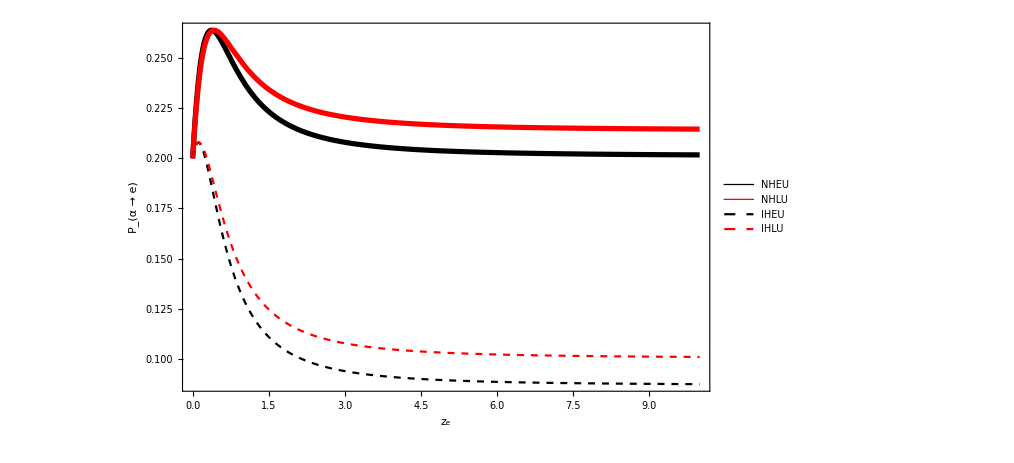

```mathematica
Plot[{newPeeNHEU[z],newPeeNHLU[z],newPeeIHEU[z],newPeeIHLU[z]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->{"NHEU","NHLU","IHEU","IHLU"},FrameLabel->{"z_e","P_(α → e)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
(*Export["/home/ali/Dropbox/NeutrinoInCurvedST/Paper3Nu_H0/PionDecay/Plot_Pα-e.pdf",%,"PDF"];*)
```

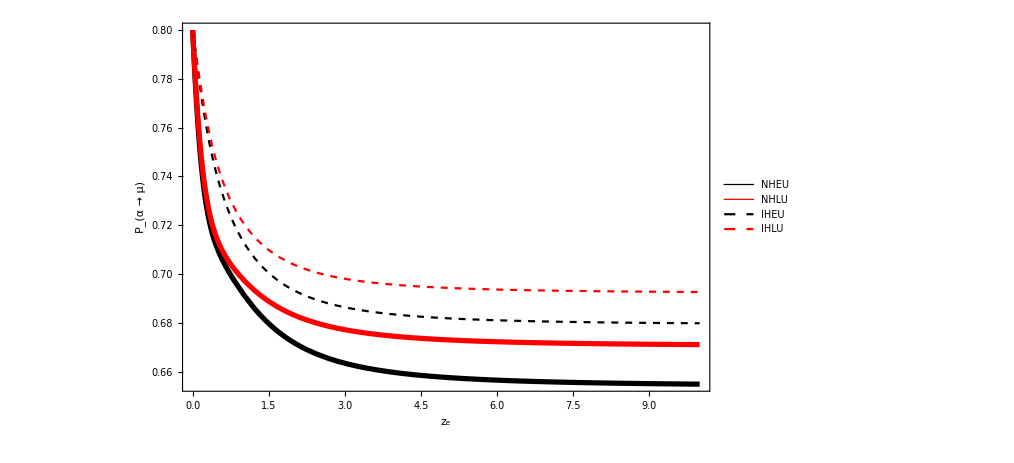

```mathematica
Plot[{newPemuNHEU[z],newPemuNHLU[z],newPemuIHEU[z],newPemuIHLU[z]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->{"NHEU","NHLU","IHEU","IHLU"},FrameLabel->{"z_e","P_(α → μ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
(*Export["/home/ali/Dropbox/NeutrinoInCurvedST/Paper3Nu_H0/PureElectron/Test/Plot_Pemu.pdf",%,"PDF"];*)
```

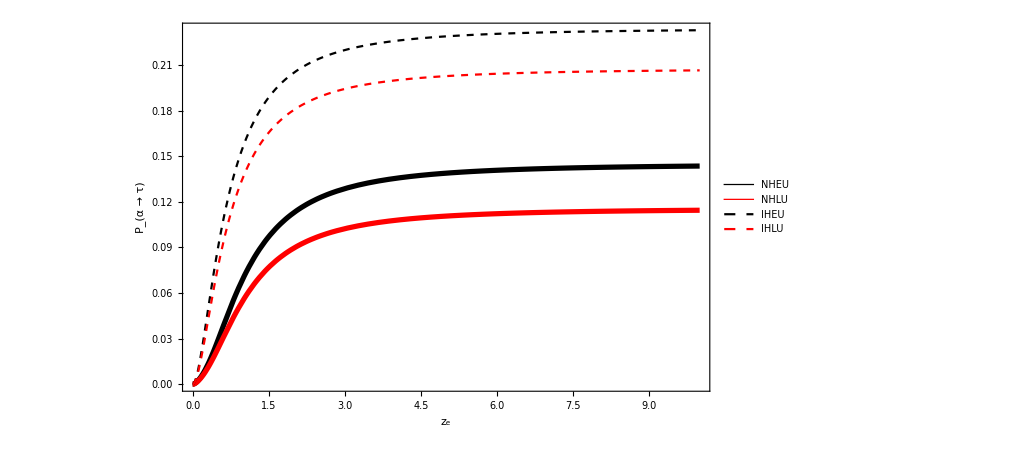

```mathematica
Plot[{newPetauNHEU[z],newPetauNHLU[z],newPetauIHEU[z],newPetauIHLU[z]},{z,0,10},ImageSize->750,Axes->False,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->{"NHEU","NHLU","IHEU","IHLU"},FrameLabel->{"z_e","P_(α → τ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
(*Export["/home/ali/Dropbox/NeutrinoInCurvedST/Paper3Nu_H0/PureElectron/Test/Plot_Petau.pdf",%,"PDF"];*)
```

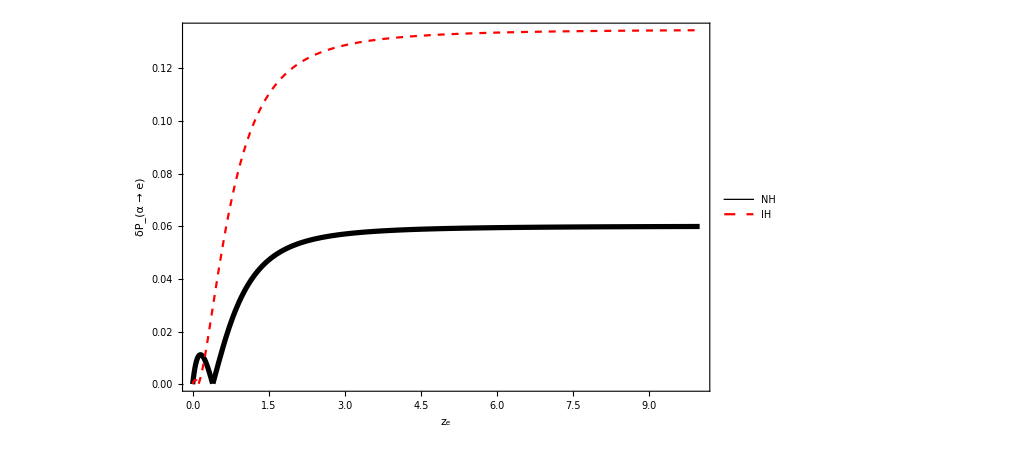

```mathematica
Plot[{Abs[(newPeeNHEU[z]-newPeeNHLU[z])/Max[newPeeNHLU[z],newPeeNHEU[z]]],Abs[(newPeeIHEU[z]-newPeeIHLU[z])/Max[newPeeIHLU[z],newPeeIHEU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->{"NH","IH"},FrameLabel->{"z_e","δP_(α → e)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
(*Export["/home/ali/Dropbox/NeutrinoInCurvedST/Paper3Nu_H0/PureElectron/Test/Plot_DiffPee.pdf",%,"PDF"];*)
```

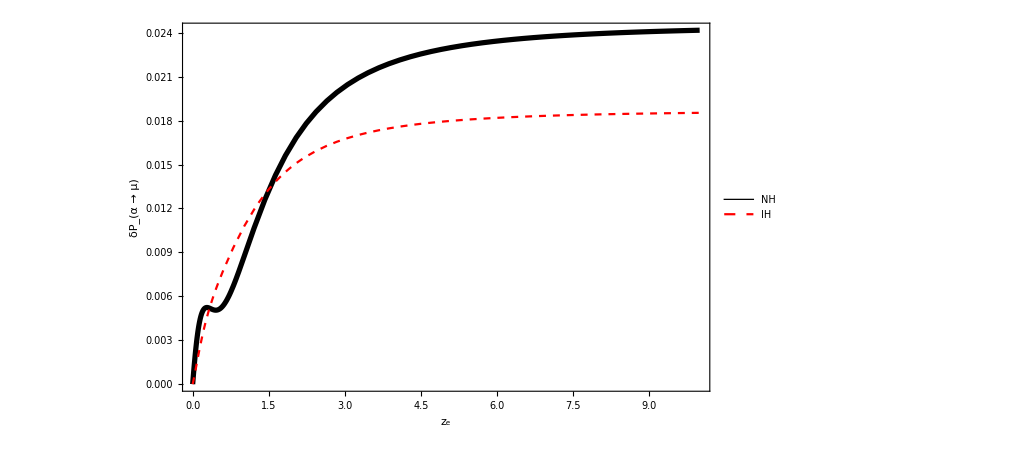

```mathematica
Plot[{Abs[(newPemuNHEU[z]-newPemuNHLU[z])/Max[newPemuNHLU[z],newPemuNHEU[z]]],Abs[(newPemuIHEU[z]-newPemuIHLU[z])/Max[newPemuIHLU[z],newPemuIHEU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->{"NH","IH"},FrameLabel->{"z_e","δP_(α → μ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
(*Export["/home/ali/Dropbox/NeutrinoInCurvedST/Paper3Nu_H0/PureElectron/Test/Plot_DiffPemu.pdf",%,"PDF"];*)
```

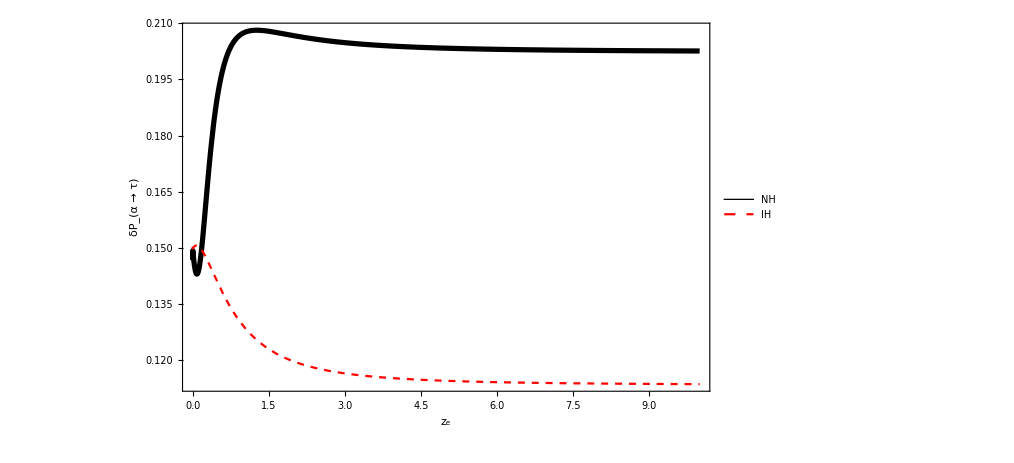

```mathematica
Plot[{Abs[(newPetauNHEU[z]-newPetauNHLU[z])/Max[newPetauNHLU[z],newPetauNHEU[z]]],Abs[(newPetauIHEU[z]-newPetauIHLU[z])/Max[newPetauIHLU[z],newPetauIHEU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->{"NH","IH"},FrameLabel->{"z_e","δP_(α → τ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
(*Export["/home/ali/Dropbox/NeutrinoInCurvedST/Paper3Nu_H0/PureElectron/Test/Plot_DiffPetau.pdf",%,"PDF"];*)
```

```mathematica
(*VALUES FOR TERNARY PLOTS*)
```

```mathematica
Print["NHEU="];
Transpose[{newPeeNHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPemuNHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauNHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]//TableForm
Print["NHLU="];
Transpose[{newPeeNHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPemuNHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauNHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]//TableForm
Print["IHEU"];
Transpose[{newPeeIHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPemuIHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauIHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]//TableForm
Print["IHLU"];
Transpose[{newPeeIHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPemuIHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauIHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]//TableForm
```

NHEU=

0.219891 | 0.779474 | 0.000635804
0.226578 | 0.772267 | 0.00115545
0.235307 | 0.76256 | 0.00213249
0.254567 | 0.738739 | 0.00669417
0.261187 | 0.709785 | 0.0290278
0.247151 | 0.697915 | 0.0549346
0.238307 | 0.691724 | 0.0699694
0.215258 | 0.671798 | 0.112944
0.205041 | 0.659551 | 0.135408

NHLU=

0.218425 | 0.781031 | 0.000544245
0.22468 | 0.77433 | 0.000990134
0.232931 | 0.765242 | 0.00182728
0.251876 | 0.742452 | 0.00567136
0.263118 | 0.713409 | 0.0234724
0.253706 | 0.702615 | 0.0436795
0.246844 | 0.697702 | 0.0554538
0.227256 | 0.683147 | 0.0895964
0.217785 | 0.674417 | 0.107799

IHEU

0.205719 | 0.791967 | 0.00231448
0.206954 | 0.788703 | 0.00434355
0.207822 | 0.783877 | 0.00830118
0.20421 | 0.769131 | 0.0266582
0.171448 | 0.7388 | 0.0897525
0.142965 | 0.721256 | 0.135779
0.129954 | 0.713263 | 0.156783
0.101711 | 0.69328 | 0.205009
0.0907741 | 0.683366 | 0.22586

IHLU

0.205394 | 0.79264 | 0.00196629
0.206647 | 0.789663 | 0.0036898
0.207684 | 0.785264 | 0.00705255
0.20552 | 0.771791 | 0.0226894
0.178936 | 0.743914 | 0.0771504
0.15422 | 0.728034 | 0.117746
0.14248 | 0.720964 | 0.136557
0.115661 | 0.703822 | 0.180518
0.10454 | 0.695568 | 0.199892